# Squeezing Eigenvalues

The purpose of the shifts in the QR “Francis” algorithm is to squeeze eigenvectors associated with eigenvalues near a chosen shift ρ to the high “j” side of a matrix A_(i,j).  The aim of this notebook is to make sure we understand what this means!

## Shifted QR Francis Algorithm

When we throw away the rotations we are not tracking the eigenvectors and the convergence is obvious.

### Dynamic Single Shift

For a single dynamic shift 
	ρ=A⟦-1,-1⟧
in a symmetric matrix the rotated matrices tend to 
	(B_1 | 0
0 | λ)
and the rotated matrix clearly has an eigenpair {λ,v} where v=e_m.

```mathematica
m=22; Id=IdentityMatrix[m]; MaxIter=8;
A0=RandomReal[{-1,1},{m,m}]; A0=A0+A0ᵀ;
{Q0,H0}=Chop[HessenbergDecomposition[A0]];
H=H0;
TabView[
Table[
ρ=H⟦m,m⟧;
{Q,R}=QRDecomposition[H-ρ Id];Q=Qᵀ;
H=Chop[R.Q+ρ Id];
MatrixPlot[H,PlotLegends->Automatic,Mesh->{{m-1},{m-1}}],
{MaxIter}]]
```

12345678

The simple single shift strategy sometimes works for non-symmetric matrices. In this case, the rotated matrices tend to 
	(B_1 | b_2
0 | λ).
The eigenvalue λ is obvious (it is sitting in the bottom corner of the matrix) but the matching eigenvector v requires a little bit of thought
	(B_1 | b_2
0 | λ).(v_1
1)=(B_1.v_1+b_2
λ)=λ(v_1
1)
So if I want to compute the eigenvector I need to solve 
	(B_1-λ 𝕀_(m-1))v_1=-b_2

```mathematica
m=22; Id=IdentityMatrix[m]; MaxIter=8;
A0=RandomReal[{-1,1},{m,m}];
{Q0,H0}=Chop[HessenbergDecomposition[A0]];
H=H0;
TabView[
Table[
ρ=H⟦m,m⟧;
{Q,R}=QRDecomposition[H-ρ Id];Q=Qᵀ;
H=Chop[R.Q+ρ Id];
MatrixPlot[H,PlotLegends->Automatic,Mesh->{{m-1},{m-1}}],
{MaxIter}], MaxIter
]
```

12345678

Lets look at the computation for the “end” eigenvector

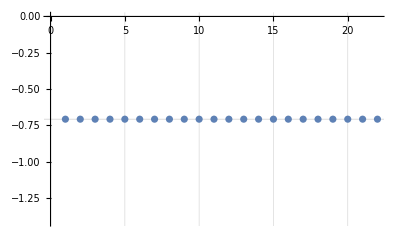

```mathematica
λ=H⟦-1,-1⟧;
B1=H⟦1;;-2,1;;-2⟧; b2=H⟦1;;-2,-1⟧;
v1=LinearSolve[B1-λ IdentityMatrix[m-1],-b2];
v=Normalize[Join[v1,{1}]];
ListPlot[(H.v)/v,GridLines->{Automatic,{λ}}]
```

So what does the “obvious” e_m have to do with anything.  It is obvious once you think about it.  It has to be an eigenvector of Hᵀ!

```mathematica
Hᵀ.SparseArray[m->1,m]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.707391}

## Messing Around

```mathematica
{m,b}={12,3};
A1=RandomReal[{-1,1},{m,m}];
A2=ConstantArray[0,{b,m}];
A2⟦-b;;-1,-b;;-1⟧=RandomReal[{-1,1},{b,b}];
APlus=ArrayFlatten[({{A1}, {A2}})];
√Eigenvalues[APlus.APlusᵀ]
Eigenvalues[A1]
```

{3.86137,2.79393,2.68616,2.18233,2.1369,1.77917,1.5905,1.46264,1.11993,0.826225,0.527134,0.29908,2.40931×10^-8,2.1401×10^-8,6.67062×10^-9}

{-2.23212+0. ⅈ,1.8968+0.283947 ⅈ,1.8968-0.283947 ⅈ,-0.0585238+1.86753 ⅈ,-0.0585238-1.86753 ⅈ,-1.08504+0.0902076 ⅈ,-1.08504-0.0902076 ⅈ,-0.214701+0.956905 ⅈ,-0.214701-0.956905 ⅈ,0.755818+0. ⅈ,-0.287352+0.34782 ⅈ,-0.287352-0.34782 ⅈ}

## Back to the Flow

### Dynamic Single Shift

For a single dynamic shift 
	{ρ1,ρ2}=Eigenvalues[A⟦-2:-1,-2:-1⟧
in a symmetric matrix the rotated matrices tend to 
	(B | 0
0 | B_2)
and the rotated matrix clearly has   eigenpairs {λ_1,v_1} and {λ_2,v_2} where
	{λ_1,λ_2}=Eigenvalues[B_2]
and the eigenvectors are obtained by padding the eigenvectors of B_2 with m-2 zeros at the front.

```mathematica
m=22; Id=IdentityMatrix[m]; MaxIter=8;
A0=RandomReal[{-1,1},{m,m}];
{Q0,H0}=Chop[HessenbergDecomposition[A0]];
H=H0;
TabView[
Table[
{ρ1,ρ2}=Eigenvalues[H⟦-2;;-1,-2;;-1⟧];
{Q,R}=QRDecomposition[H-ρ1 Id];Q=Qᵀ;
H=Chop[R.Q+ρ1 Id];
{Q,R}=QRDecomposition[H-ρ2 Id];Q=Qᵀ;
H=Chop[R.Q+ρ2 Id];
MatrixPlot[H,PlotLegends->Automatic],
{MaxIter}]]
```

12345678

```mathematica
1+1
```

2

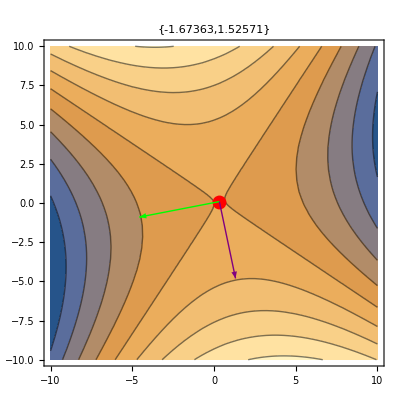

```mathematica
n=2;
A=RandomReal[{-1,1},{n,n}];
g=RandomReal[{-1,1},n];
A=A+Transpose[A];
x=LinearSolve[A,-g];
MatrixForm[A];
{{λ1,λ2},{v1,v2}}=Eigensystem[A];
ContourPlot[0.5*{x1,x2}.A.{x1,x2}+g.{x1,x2},{x1,-10,10},{x2,-10,10},
PlotLabel->{λ1,λ2},
Epilog->{
{Red, PointSize[.025],Point[x]},
{Green, Arrow[{x,x+5*v1}]},
{Purple,Arrow[{x,x+5*v2}]}
}]
```